# 知識構造化法

2013年度　秋学期、筑波大学　学部3・4年次、5・6限

## 2.データの構造について

### 純関数

```mathematica
f[][3,2]/.{f[]->Function[{x,y},x y]}
```

6

```mathematica
FullForm[f']
```

Derivative[1][f]

```mathematica
FullForm[f'[x]]
```

Derivative[1][f][x]

```mathematica
Derivative[1][x^3][x]
```

(x^3)'[x]

```mathematica
Derivative[1][Function[u,u^3]][x]
```

3 x^2

```mathematica
Derivative[1][Function[x,x^3]][x]
```

3 x^2

```mathematica
D[Function[u, u^3][x],x]
```

3 x^2

```mathematica
D[x^3,x]
```

3 x^2

```mathematica
FullForm[Hold[D[x^3,x]]]
```

Hold[D[Power[x,3],x]]

## 4.探索的データ解析

### 二重指数関数

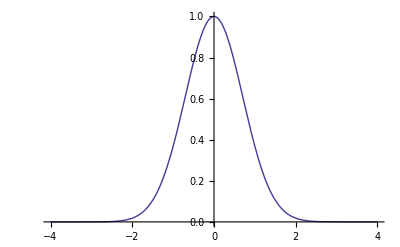

```mathematica
Plot[E^-(x^2),{x,-4,4}]
```

```mathematica
Integrate[E^-(x^2),{x,-Infinity,Infinity}]
```

√π

```mathematica
Integrate[E^-(-m+x^2),{x,-Infinity,Infinity}]
```

ⅇ^m √π

```mathematica
Integrate[E^-((-m+x^2)/(2s^2)),{x,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(m/(2 s^2)) √(2 π))/(√(1/s^2)),Re[s^2]>0]

```mathematica
Solve[D[D[E^-(s^2 x^2),x],x]==0,{x}]
```

{{x→-1/(√2 s)},{x→1/(√2 s)}}

### 正規分布

```mathematica
PDF[NormalDistribution[m,s], x]
```

(ⅇ^(-(-m+x)^2/(2 s^2)))/(√(2 π) s)

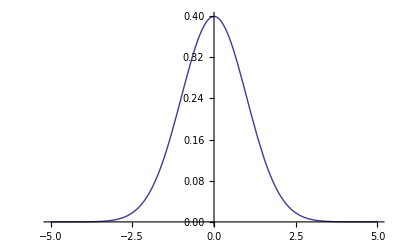

```mathematica
Plot[PDF[NormalDistribution[],x],{x,-5,5}]
```

```mathematica
Integrate[PDF[NormalDistribution[],x],{x,-Infinity,Infinity}]
```

1

```mathematica
Solve[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{x→m-s},{x→m+s}}

```mathematica
Reduce[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

s≠0&&(x==m+s||x==m-s)

```mathematica
Integrate[PDF[NormalDistribution[0,1], x],x]
```

1/2 Erf[x/(√2)]

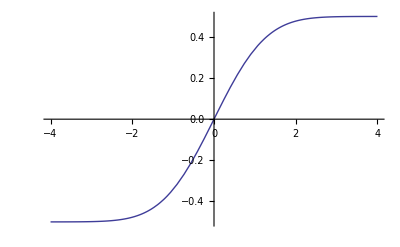

```mathematica
Plot[Integrate[PDF[NormalDistribution[0,1], x],x]/.{x->t},{t,-4,4}]
```

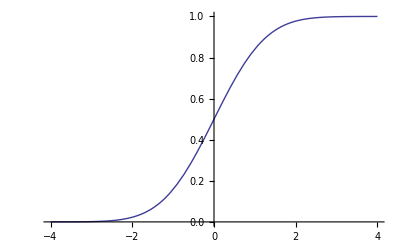

```mathematica
Plot[CDF[NormalDistribution[0,1], x]/.{x->t},{t,-4,4}]
```

### その他

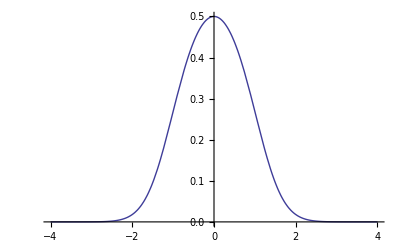

```mathematica
Plot[1/(1+E^(x^2)),{x,-4,4}]
```

```mathematica
Integrate[1/(1+E^(x^2)),{x,-Infinity,Infinity}]
```

-(-1+√2) √π Zeta[1/2]

### ランダムネス

一様乱数

```mathematica
ra=Table[Random[],{400}];
```

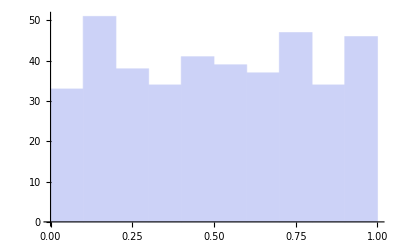

```mathematica
Histogram[ra]
```

一様乱数から分布を作る -CDF-

```mathematica
CDF[NormalDistribution[0,1]]//FullForm
```

Function[Times[Erfc[Times[Plus[0,Times[-1,Slot[1]]],Power[Times[Sqrt[2],1],-1]]],Power[2,-1]]]

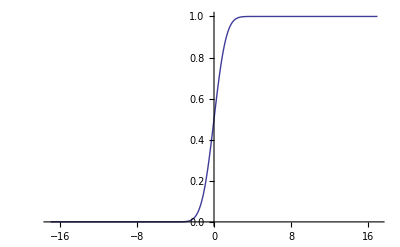

```mathematica
Plot[(1/2 Erfc[(0-#1)/(√2 1)]&)[x],{x,-16.970562748477143,16.970562748477143}]
```

```mathematica
ifc:=InverseFunction[CDF[NormalDistribution[0,1]]]
```

```mathematica
ira=Map[ifc[#//N]&,ra];
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

General::stop: この計算中に，InverseFunction :: ifunのこれ以上の出力は表示されません．

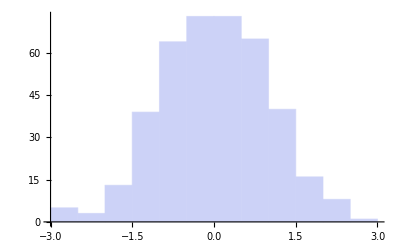

```mathematica
Histogram[ira]
```

一様乱数から分布を作る -PDF-

```mathematica
PDF[NormalDistribution[0, 1]]
```

Exp[-1/2 ((#1-0) 1/1)^2]/(1 √(2 π))&

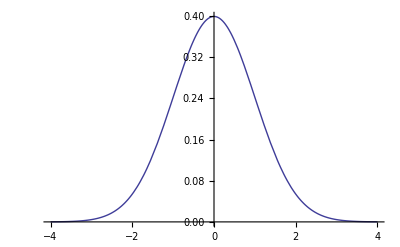

```mathematica
Plot[(Exp[-1/2 ((#1-0) 1/1)^2]/(1 √(2 π))&)[x],{x,-4,4}]
```

```mathematica
Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]
```

1/2 (1+Erf[t/(√2)])

```mathematica
Function[Evaluate[Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]/.t->#]]
```

1/2 (1+Erf[#1/(√2)])&

```mathematica
Plot[(1/2 (1+Erf[#1/(√2)])&)[x],{x,-16.970562748477143,16.970562748477143}]
```

-Graphics-

```mathematica
ifp:=InverseFunction[Function[Evaluate[Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]/.t->#]]]
```

```mathematica
ifp[0.2]
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

-0.841621

```mathematica
ira=Map[ifp[#//N]&,ra];
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

General::stop: この計算中に，InverseFunction :: ifunのこれ以上の出力は表示されません．

```mathematica
ira[[1]]
```

-0.212023

```mathematica
Histogram[ira,10]
```

-Graphics-

## 8.自己組織化マップ

### ニューラルネットワーク

#### ニューロン

加算器

```mathematica
adder[o_List,w_List]:=Tr[w*o]
```

```mathematica
adder[{1,2,3},{a,b,c}]
```

a+2 b+3 c

入出力関数 -シグモイド関数-

```mathematica
SGM[a_,th_]:=1/(1+E^(-a+th))
```

```mathematica
Plot3D[SGM[in,t],{in,-10,10},{t,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

ニューロンの設計

```mathematica
NER[o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],th]>=th,1,0]
```

```mathematica
ner[o_List,w_List,iofunc_,th_]:=iofunc[adder[o,w],th]
```

加算器と入出力関数(iofunc)を組み合わせニューロンを作る。
入出力関数(iofunc)は、いま、シグモイド(0 < SGM < 1)に定義されている。
かつ、ニューロン(NER)は、非線形活性化関数として機能している。
しきい値 th は、iofunc() そのものにも影響するかたちになっている。

設計したニューロンの性質:

入力を{1,1,1}、重みを{10,10,10}とする。

当然ながら、thに1より大きい値を設定すると、ニューロンの出力は、かならず 0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

当然ながら、thに0より小さい値を設定すると、ニューロンの出力は、かならず 1。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

つまり、シグモイドを採る理由は、しきい値の範囲を決めるため、と解釈してもよい。

次に、重みをすべて負の値とし、thを0 <= th <= 1の間で変化させる。thが0の場合のみ、ニューロンの出力は1。

```mathematica
Table[{NER[{1,1,1},{-1,-1,-1},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

重みをすべて大きな正の値とし、thを0 <= th <= 1の間で変化させる。thが1に非常に近い場合にのみ、ニューロンの出力は0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.

#### 教師あり学習

ニューラルネットワークの簡単な例:

-Graphics-

学習データ: {<入力ベクトル>,<期待される出力>}

```mathematica
ldata1={
{{0,0},0},
{{1,0},0},
{{0,1},0},
{{1,1},1}
}
```

{{{0,0},0},{{1,0},0},{{0,1},0},{{1,1},1}}

```mathematica
TableForm[Map[Flatten[#]&,ldata1],TableHeadings->{Table[n,{n,4}],{"入力１","入力２","出力(期待)"}}]
```

| 入力１ | 入力２ | 出力(期待)
1 | 0 | 0 | 0
2 | 1 | 0 | 0
3 | 0 | 1 | 0
4 | 1 | 1 | 1

重みベクトル、しきい値の初期値

```mathematica
wdata[0]={1.5,-1.0}
```

{1.5,-1.}

```mathematica
thh[0]=0.8
```

0.8

```mathematica
NER[ldata1[[1,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[2,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[3,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0

上の例では、パターン4のときに期待する値が得られていない。

学習:

重みとしきい値を変化させ、学習をおこなう。

しきい値を小さくすれば、出力は大きくなる。

```mathematica
delta=.
```

```mathematica
thh[0]
```

0.8

```mathematica
ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0.425557

```mathematica
delta[1]=ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]-thh[0]
```

-0.374443

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]+delta[1]]
```

1

入力に対応する重みを大きくすれば、出力は大きくなる。

```mathematica
wdata[0]
```

{1.5,-1.}

```mathematica
NER[ldata1[[4,1]],wdata[0]+0.5*ldata1[[4,1]],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0]+(0.5+0.5)*ldata1[[4,1]],SGM,thh[0]]
```

1

入力がない場合、しきい値を変化させ、入力がある場合、それに対応する重みを変化させることによって学習を行う。どの程度変化させるか -> デルタルールなど。

#### 分類機械と競合学習

分類機械:入力のパターンを出力の個数に分類する。出力の受ける入力の重みの総和は1。

-Graphics-

∑ w_i,1 = 1 ; ∑ w_i,2 = 1

競合学習の手順:

重みの初期値:

```mathematica
wmat[0]={
{0.5,0.5},
{0.6,0.4}
}
```

{{0.5,0.5},{0.6,0.4}}

```mathematica
TableForm[wmat[0],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.6 | 0.4

入力パターン:

```mathematica
pdata1={
{1,0},
{0,1},
{1,1},
{1,0}
}
```

{{1,0},{0,1},{1,1},{1,0}}

```mathematica
TableForm[pdata1,TableHeadings->{Table[i,{i,4}],{"入力1","入力2"}}]
```

| 入力1 | 入力2
1 | 1 | 0
2 | 0 | 1
3 | 1 | 1
4 | 1 | 0

勝者に対する重みの変化量:
dw = l (c/n - w) ; l : 学習率、c : 入力値、n : 入力数、w : 現在の重み

学習係数 lを0.5に。

```mathematica
l=0.5
```

0.5

入力パターン1に対して学習:

入力パターン1の場合の出力1:

```mathematica
pdata1[[1]] wmat[0][[1]]//Tr
```

0.5

入力パターン1の場合の出力2:

```mathematica
pdata1[[1]] wmat[0][[2]]//Tr
```

0.6

出力2が勝者となる

そこで、w_2,1とw_2,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.6 | 0.4

```mathematica
dw[1][1,1]=0
```

0

```mathematica
dw[1][1,2]=0
```

0

まず、wd_2,1(出力2入力1)

pdata1[[1,1]] : パターン1:入力1
Tr[pdata1[[1]]] : パターン1:出力2への入力数
wmat[0][[2,1]] : パターン1:出力2、入力1のとき

```mathematica
dw[1][2,1]=l(pdata1[[1,1]]/Tr[pdata1[[1]]]-wmat[0][[2,1]])
```

0.2

つぎに、wd_2,2(出力2入力2)

pdata1[[1,2]] : パターン1:入力2
Tr[pdata1[[1]]] : パターン1:出力2への入力数
wmat[0][[2,2]] : パターン1:出力2、入力2のとき

```mathematica
dw[1][2,2]=l(pdata1[[1,2]]/Tr[pdata1[[1]]]-wmat[0][[2,2]])
```

-0.2

重みを更新:

```mathematica
wmat[0]
```

{{0.5,0.5},{0.6,0.4}}

```mathematica
wmat[1]=wmat[0]+{{dw[1][1,1],dw[1][1,2]},{dw[1][2,1],dw[1][2,2]}}
```

{{0.5,0.5},{0.8,0.2}}

```mathematica
TableForm[wmat[1],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

入力パターン2に対して学習:

入力パターン2の場合の出力1:

```mathematica
pdata1[[2]] wmat[1][[1]]//Tr
```

0.5

入力パターン1の場合の出力2:

```mathematica
pdata1[[2]] wmat[1][[2]]//Tr
```

0.2

出力1が勝者となる

そこで、w_1,1とw_1,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

```mathematica
dw[2][2,1]=0
```

0

```mathematica
dw[2][2,2]=0
```

0

まず、wd_1,1(出力1入力1)

pdata1[[2,1]] : パターン2:入力1
Tr[pdata1[[2]]] : パターン2:出力1への入力数
wmat[1][[1,1]] : パターン2:出力1、入力1のとき

```mathematica
dw[2][1,1]=l(pdata1[[2,1]]/Tr[pdata1[[2]]]-wmat[1][[1,1]])
```

-0.25

つぎに、wd_1,2(出力1入力2)

pdata1[[2,2]] : パターン2:入力2
Tr[pdata1[[2]]] : パターン2:出力1への入力数
wmat[1][[1,2]] : パターン2:出力1、入力2のとき

```mathematica
dw[2][1,2]=l(pdata1[[2,2]]/Tr[pdata1[[2]]]-wmat[1][[1,2]])
```

0.25

重みを更新:

```mathematica
wmat[1]
```

{{0.5,0.5},{0.8,0.2}}

```mathematica
wmat[2]=wmat[1]+{{dw[2][1,1],dw[2][1,2]},{dw[2][2,1],dw[2][2,2]}}
```

{{0.25,0.75},{0.8,0.2}}

```mathematica
TableForm[wmat[2],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.25 | 0.75
出力2 | 0.8 | 0.2

入力パターン3に対して学習:

入力パターン3の場合の出力1:

```mathematica
pdata1[[3]] wmat[2][[1]]//Tr
```

1.

入力パターン3の場合の出力2:

```mathematica
pdata1[[3]] wmat[2][[2]]//Tr
```

1.

双方を勝者として学習させる。

そこで、w_1,1とw_1,2、w_2,1とw_2,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

まず、wd_1,1(出力1入力1)

pdata1[[3,1]] : パターン3:入力1
Tr[pdata1[[3]]] : パターン3:出力1への入力数
wmat[2][[1,1]] : パターン3:出力1、入力1のとき

```mathematica
dw[3][1,1]=l(pdata1[[3,1]]/Tr[pdata1[[3]]]-wmat[2][[1,1]])
```

0.125

つぎに、wd_1,2(出力1入力2)

pdata1[[3,2]] : パターン3:入力2
Tr[pdata1[[3]]] : パターン3:出力1への入力数
wmat[2][[1,2]] : パターン3:出力1、入力2のとき

```mathematica
dw[3][1,2]=l(pdata1[[3,2]]/Tr[pdata1[[3]]]-wmat[2][[1,2]])
```

-0.125

つぎに、wd_2,1(出力2入力1)

pdata1[[3,1]] : パターン3:入力1
Tr[pdata1[[3]]] : パターン3:出力2への入力数
wmat[2][[2,1]] : パターン3:出力2、入力1のとき

```mathematica
dw[3][2,1]=l(pdata1[[3,1]]/Tr[pdata1[[3]]]-wmat[2][[2,1]])
```

-0.15

つぎに、wd_2,2(出力2入力2)

pdata1[[3,2]] : パターン3:入力2
Tr[pdata1[[3]]] : パターン3:出力2への入力数
wmat[2][[2,2]] : パターン3:出力2、入力2のとき

```mathematica
dw[3][2,2]=l(pdata1[[3,2]]/Tr[pdata1[[3]]]-wmat[2][[2,2]])
```

0.15

重みを更新:

```mathematica
wmat[2]
```

{{0.25,0.75},{0.8,0.2}}

```mathematica
wmat[3]=wmat[2]+{{dw[3][1,1],dw[3][1,2]},{dw[3][2,1],dw[3][2,2]}}
```

{{0.375,0.625},{0.65,0.35}}

```mathematica
TableForm[wmat[3],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.65 | 0.35

入力パターン4に対して学習:

入力パターン4の場合の出力1:

```mathematica
pdata1[[4]] wmat[3][[1]]//Tr
```

0.375

入力パターン4の場合の出力2:

```mathematica
pdata1[[4]] wmat[3][[2]]//Tr
```

0.65

出力2が勝者となる。

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.65 | 0.35

そこで、w_2,1とw_2,2を変化させる。

```mathematica
dw[4][1,1]=0
```

0

```mathematica
dw[4][1,2]=0
```

0

まず、wd_2,1(出力2入力1)

pdata1[[4,1]] : パターン4:入力1
Tr[pdata1[[4]]] : パターン4:出力2への入力数
wmat[3][[2,1]] : パターン4:出力2、入力1のとき

```mathematica
dw[4][2,1]=l(pdata1[[4,1]]/Tr[pdata1[[4]]]-wmat[3][[2,1]])
```

0.175

つぎに、wd_2,2(出力2入力2)

pdata1[[4,2]] : パターン4:入力2
Tr[pdata1[[4]]] : パターン4:出力2への入力数
wmat[3][[2,2]] : パターン4:出力2、入力2のとき

```mathematica
dw[4][2,2]=l(pdata1[[4,2]]/Tr[pdata1[[4]]]-wmat[3][[2,2]])
```

-0.175

重みを更新:

```mathematica
wmat[3]
```

{{0.375,0.625},{0.65,0.35}}

```mathematica
wmat[4]=wmat[3]+{{dw[4][1,1],dw[4][1,2]},{dw[4][2,1],dw[4][2,2]}}
```

{{0.375,0.625},{0.825,0.175}}

```mathematica
TableForm[wmat[4],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.825 | 0.175

学習後、分類機械として利用:

パターン1:

```mathematica
pdata1[[1]] wmat[4][[1]]//Tr
```

0.375

```mathematica
pdata1[[1]] wmat[4][[2]]//Tr
```

0.825

パターン2:

```mathematica
pdata1[[2]] wmat[4][[1]]//Tr
```

0.625

```mathematica
pdata1[[2]] wmat[4][[2]]//Tr
```

0.175

パターン3:

```mathematica
pdata1[[3]] wmat[4][[1]]//Tr
```

1.

```mathematica
pdata1[[3]] wmat[4][[2]]//Tr
```

1.

パターン4:

```mathematica
pdata1[[4]] wmat[4][[1]]//Tr
```

0.375

```mathematica
pdata1[[4]] wmat[4][[2]]//Tr
```

0.825

#### 自己組織化マップ

パワーポイントファイル：知識構造化法_天野加筆9-2.pptx

## 9.主成分分析と数量化III類・IV類

### 分散共分散

ベクトルaを仮定

```mathematica
Array[a,{3}]
```

{a[1],a[2],a[3]}

Mathematicaによる分散の計算：

```mathematica
Variance[Array[a,{3}]]
```

1/6 ((2 a[1]-a[2]-a[3]) Conjugate[a[1]]+(-a[1]+2 a[2]-a[3]) Conjugate[a[2]]+(-a[1]-a[2]+2 a[3]) Conjugate[a[3]])

分散(ベクトルaのドメインをRealに限定)：

```mathematica
(Variance[Array[a,{3}]]//Expand)/.Conjugate[x_]->x
```

a[1]^2/3-1/3 a[1] a[2]+a[2]^2/3-1/3 a[1] a[3]-1/3 a[2] a[3]+a[3]^2/3

確認：Mathematicaでは(n-1)で割っている。

```mathematica
Tr[(Array[a,{3}]-(Array[a,{3}]//Mean))^2]/(3-1)//Expand
```

a[1]^2/3-1/3 a[1] a[2]+a[2]^2/3-1/3 a[1] a[3]-1/3 a[2] a[3]+a[3]^2/3

分散共分散：

```mathematica
Covariance[Array[a,{3,3}]]//MatrixForm
```

(1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,1]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,1]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,2]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,2]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,3]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,3]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,3]])
1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,1]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,1]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,2]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,2]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,3]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,3]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,3]])
1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,1]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,1]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,2]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,2]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,3]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,3]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,3]]))

```mathematica
Covariance[Array[a,{3,3}]]/.Conjugate[x_]->x//MatrixForm
```

(1/6 (a[1,1] (2 a[1,1]-a[2,1]-a[3,1])+a[2,1] (-a[1,1]+2 a[2,1]-a[3,1])+a[3,1] (-a[1,1]-a[2,1]+2 a[3,1])) | 1/6 (a[1,2] (2 a[1,1]-a[2,1]-a[3,1])+a[2,2] (-a[1,1]+2 a[2,1]-a[3,1])+(-a[1,1]-a[2,1]+2 a[3,1]) a[3,2]) | 1/6 (a[1,3] (2 a[1,1]-a[2,1]-a[3,1])+a[2,3] (-a[1,1]+2 a[2,1]-a[3,1])+(-a[1,1]-a[2,1]+2 a[3,1]) a[3,3])
1/6 (a[1,1] (2 a[1,2]-a[2,2]-a[3,2])+a[2,1] (-a[1,2]+2 a[2,2]-a[3,2])+a[3,1] (-a[1,2]-a[2,2]+2 a[3,2])) | 1/6 (a[1,2] (2 a[1,2]-a[2,2]-a[3,2])+a[2,2] (-a[1,2]+2 a[2,2]-a[3,2])+a[3,2] (-a[1,2]-a[2,2]+2 a[3,2])) | 1/6 (a[1,3] (2 a[1,2]-a[2,2]-a[3,2])+a[2,3] (-a[1,2]+2 a[2,2]-a[3,2])+(-a[1,2]-a[2,2]+2 a[3,2]) a[3,3])
1/6 (a[1,1] (2 a[1,3]-a[2,3]-a[3,3])+a[2,1] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,1] (-a[1,3]-a[2,3]+2 a[3,3])) | 1/6 (a[1,2] (2 a[1,3]-a[2,3]-a[3,3])+a[2,2] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,2] (-a[1,3]-a[2,3]+2 a[3,3])) | 1/6 (a[1,3] (2 a[1,3]-a[2,3]-a[3,3])+a[2,3] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,3] (-a[1,3]-a[2,3]+2 a[3,3])))

### 数量化III類

```mathematica
quant3[data_]:=
 Module[{n,m,f,g,T,A,B,S,v,r,u,y,x},
  n=Length[data];
  m=Length[data[[1]]];
  f[i_]:=Apply[Plus,Table[data[[i,t]],{t,1,m}]];
  g[j_]:=Apply[Plus,Table[data[[s,j]],{s,1,n}]];
  T=Apply[Plus,Table[f[i],{i,1,n}]];
  A=N[Table[data[[t,s]]/Sqrt[g[s]],{s,1,m},{t,1,n}]];
  B=N[Table[data[[t,s]]/f[t]/Sqrt[g[s]],{t,1,n},{s,1,m}]];
  S=A.B;
  v=Eigenvalues[S];
  r=Sqrt[v];
  u=Eigenvectors[S];
  y[p_]:=Table[N[u[[p,k]] Sqrt[T]/Sqrt[g[k]]],{k,1,m}];
  x[q_]:=N[B.u[[q]] Sqrt[T]/Sqrt[v[[q]]]];
  {v,y[2],x[2]}
 ];
```

### 数量化IV類

```mathematica
quant4[nn_List]:=
 Module[{lnn, nn1, n2, zz, zz2, nn2, esnn2},
  lnn = Length[nn];
  nn1 = Table[nn[[i,j]]+nn[[j,i]],{i,lnn},{j,lnn}];
  n2 = Plus @@ nn1;
  zz = Table[0,{lnn},{lnn-1}];
  zz2 = Table[Insert[zz[[k]],-n2[[k]],k],{k,lnn}];
  nn2 = N[nn1+zz2];
  esnn2 = Eigensystem[nn2];
  {nn1, n2, zz, zz2, nn2, esnn2}
 ];
```

## 計算メモ

-Graphics-

-Graphics-